```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
StartSet={31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29};
```

```mathematica
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
];
```

```mathematica
IS1=Exch[{StartSet,StartSet/.S1/.S1/.S1}];
IS2=Exch[{StartSet,StartSet/.S2/.S2/.S2}];
IS3=Exch[{StartSet,StartSet/.S3/.S3/.S3}];
IS4=Exch[{StartSet,StartSet/.S4/.S4/.S4}];
IS5=Exch[{StartSet,StartSet/.S5/.S5/.S5}];
IS6=Exch[{StartSet,StartSet/.S6/.S6/.S6}];
IS7=Exch[{StartSet,StartSet/.S7/.S7/.S7}];
IS8=Exch[{StartSet,StartSet/.S8/.S8/.S8}];
IS9=Exch[{StartSet,StartSet/.S9/.S9/.S9}];
```

```mathematica
prmt(*mypermutation*)={S1,S2,S3,S4,S5,S6,S7,S8,S9,IS1,IS2,IS3,IS4,IS5,IS6,IS7,IS8,IS9};
```

```mathematica
Place[Lst_,Rndm_]:=Module[{tr={},p={}},tr=Array[Lst[[1,#2]]≥ Rndm>Sign[#2-1]Lst[[1,#2-1]]&,{1,18}];
p=Flatten[Position[tr[[1]],True],1];p[[1]]](*选择第p条路, Lst:{{...}}, Rndm: Num*)
AntTrace[Prbblt_,rndmst_,trnslng_]:=Module[{trc={}},AppendTo[trc,Place[{Prbblt[[1]]},rndmst[[1]]]];For[i=1,i≤trnslng-1,i++,AppendTo[trc,Place[{Prbblt[[2,i,Last[trc]]]},rndmst[[1+i]]]]];trc];(*返回蚂蚁的路径, Prbblt:{
{...},
{
{{...}...{...}},{...}...{...}
}
}, rndmst:{...}*)
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
];(*变换公式, List:{Start,End}*)
PermulateMultiply[Srtst_,List_]:=Module[{Cntr=Srtst,ndSt={}},For[i=1,i≤Length[List],i++,Cntr=Cntr/.prmt[[List[[i]]]]];ndSt=Exch[{StartSet,Cntr}]];(*Srtst:StartSet, List: AntTrace[...]*)
```

```mathematica
ExtractSet[StartSet_,Tans_]:=Module[{StrtSt=StartSet,ndSt={},myi=1},ndSt=StrtSt/.Tans;
While[myi≤Length[StrtSt],If[StrtSt[[myi]]==ndSt[[myi]],StrtSt=Delete[StrtSt,myi];ndSt=Delete[ndSt,myi];myi--];myi++];
{StrtSt,ndSt}
];
```

```mathematica
TnsFrm[StartSet_,Tans_]:=Module[{keepp={},pic=Array[{}&,6],xtrctSt={},i=1,j=1},
pic[[1]]=Flatten[Table[{FaceForm[Blue,Texture[-Graphics-]],Polygon[{{i-1,j-1,0},{i-1,j,0},{i,j,0},{i,j-1,0}}]},{j,3},{i,3}],1];
pic[[2]]=Flatten[Table[{FaceForm[White,Texture[-Graphics-]],Polygon[{{i-1,j,3},{i-1,j-1,3},{i,j-1,3},{i,j,3}}]},{j,3},{i,3}],1];
pic[[3]]=Flatten[Table[{FaceForm[Green,Texture[-Graphics-]],Polygon[{{i-1,3,j-1},{i-1,3,j},{i,3,j},{i,3,j-1}}]},{j,3},{i,3}],1];
pic[[4]]=Flatten[Table[{FaceForm[Red,Texture[-Graphics-]],Polygon[{{i-1,0,j},{i-1,0,j-1},{i,0,j-1},{i,0,j}}]},{j,3},{i,3}],1];
pic[[5]]=Flatten[Table[{FaceForm[Yellow,Texture[-Graphics-]],Polygon[{{0,3-j,i-1},{0,3-j,i},{0,4-j,i},{0,4-j,i-1}}]},{i,3},{j,3}],1];
pic[[6]]=Flatten[Table[{FaceForm[Purple,Texture[-Graphics-]],Polygon[{{3,3-j,i},{3,3-j,i-1},{3,4-j,i-1},{3,4-j,i}}]},{i,3},{j,3}],1];

xtrctSt=IntegerDigits[ExtractSet[StartSet,Tans]];
For[i=1,i≤Length[xtrctSt[[1]]],i++,AppendTo[keepp,pic[[xtrctSt[[1,i,1]],xtrctSt[[1,i,2]],1]]]];
For[i=1,i≤Length[xtrctSt[[1]]],i++,pic[[xtrctSt[[2,i,1]],xtrctSt[[2,i,2]],1]]=keepp[[i]]];
Print[Graphics3D[pic,Lighting->Automatic]];
];
```

```mathematica
Ant[StartPermulate_,Prbblt_,rndmst_,Lngthn_,trypic_,trnslng_]:=Module[{trace={},Trans={},p=0,x={},l=0,prbbl=Prbblt,kuosan=1/8192,mygraph={},releaseform={},StrtSt=StartSet/.StartPermulate},
trace=AntTrace[prbbl,rndmst,trnslng](*蚂蚁的轨迹*);Trans=PermulateMultiply[StrtSt,trace];
l=Length[Trans];p=trace[[1]];If[l==0,l=50;Print["l=0,reset l=50"]];
x=Differences[Flatten[{0,prbbl[[1]]}]];x[[p]]+=2/l;x+=kuosan(*气味飘散*);
prbbl[[1]]=Accumulate[x/Total[x]];
For[i=1,i≤trnslng-1,i++,p=trace[[1+i]];x=Differences[Flatten[{0,prbbl[[2,i,trace[[i]]]]}]];x[[p]]+=2/l;x+=kuosan(*气味飘散*);prbbl[[2,i,trace[[i]]]]=Accumulate[x/Total[x]]];
releaseform=Table[If[trace[[i]]≤9,trace[[i]],-(trace[[i]]-9)],{i,trnslng}];(*书面形式处理*)
mygraph={Table[{i,trace[[i]]},{i,trnslng}]};(*mygraph=Flatten[AppendTo[mygraph,Table[{i,j},{j,18},{i,trnslng}]],1];*)

If[trypic==0∧Length[Trans]≤Lngthn,Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]]](*书面写法*);
If[trypic==1,Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]];(*树形图*)
If[trypic==2,Print[ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400]]];(*路径图*)
If[trypic==3,Print[BarChart[{prbbl[[1]]}∪Table[prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]];(*直方图*)
If[trypic==4,Print[ListLinePlot[{prbbl[[1]]}∪Table[ii/1.25 prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]];(*概率的折线图*)
If[trypic==5∧Length[Trans]≤Lngthn,
Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]];
Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400],
ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400],
BarChart[{prbbl[[1]]}∪Table[prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]
];
If[trypic==6∧Length[Trans]≤Lngthn,
Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]];
Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400],
ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400],
ListLinePlot[{prbbl[[1]]}∪Table[ii/1.25 prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],PlotMarkers->Automatic,ImageSize->400]]
];
If[trypic==7∧Length[Trans]≤Lngthn,TnsFrm[StartSet,Trans];Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]];
Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]];

{prbbl,Min[l,Lngthn]}]
```

```mathematica
(*概率空间的构造*)
translength=18;(*变换次数*)
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,translength-1}]];
prbblt=N[prbblt];
(*prbblt[[1]]和prbblt[[2]], prbblt[[2]]有8个步, 每步18种已达到的路线, 每种路线有18种候选路线*)
trnslngth=50;(*最终变换最初不超过50个长度*)
times=AbsoluteTime[DateList[]];
StrtPrmlt={15->65,65->25,25->55,55->15,16->66,66->22,22->28,28->56,56->58,58->62,62->46,46->48,48->38,38->44,44->24,24->16,18->36,36->26,26->32,32->64,64->68,68->18,19->39,39->27,27->61,61->67,67->57,57->33,33->29,29->37,37->19,23->49,49->69,69->23};
DateList[]
While[trnslngth≥ 4∧AbsoluteTime[DateList[]]-times≤20*60,rndmst=RandomReal[1,translength](*随机路径*);{prbblt,trnslngth}=Ant[StrtPrmlt,prbblt,rndmst,trnslngth,7,translength]]
DateList[]
```

```mathematica
issss=ToExpression[Import["F:\\data\\issss.txt","Data"]];
sssis=ToExpression[Import["F:\\data\\sssis.txt","Data"]];
ssis=ToExpression[Import["F:\\data\\ssis.txt","Data"]];
isss=ToExpression[Import["F:\\data\\isss.txt","Data"]];
isiss=ToExpression[Import["F:\\data\\isiss.txt","Data"]];
sisis=ToExpression[Import["F:\\data\\sisis.txt","Data"]];
issssisis=ToExpression[Import["F:\\data\\issssisis.txt","Data"]];
isissssisiss=ToExpression[Import["F:\\data\\isissssisiss.txt","Data"]];
isissssisisslessfifteen=ToExpression[Import["F:\\data\\isissssisisslessfifteen.txt","Data"]];
isssssis=ToExpression[Import["F:\\data\\isssssis.txt","Data"]];
isssssislessfifteen=ToExpression[Import["F:\\data\\isssssislessfifteen.txt","Data"]];
```

```mathematica
space={};kp=issssisis;
For[i=1,i≤Length[kp],i++,space=space∪{kp[[i,1]]}]
try={12->48,15->65,18->42,22->38,25->55,28->32,32->12,35->45,37->67,38->18,39->57,42->22,45->35,48->28,55->25,57->39,65->15,67->37};
MemberQ[space,try]
```

False

```mathematica
(*概率空间的构造*)
translength=8;(*变换次数*)
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,translength-1}]];
prbblt=N[prbblt];
(*prbblt[[1]]和prbblt[[2]], prbblt[[2]]有8个步, 每步18种已达到的路线, 每种路线有18种候选路线*)
trnslngth=35;(*最终变换最初不超过50个长度*)
times=AbsoluteTime[DateList[]];
StrtPrmlt={11->39,14->56,16->34,17->59,18->14,19->61,21->41,22->32,27->51,28->48,29->57,31->21,32->52,33->19,34->28,37->31,38->22,39->37,41->29,44->62,47->11,48->18,51->47,52->44,53->67,54->38,56->16,57->17,59->53,61->33,62->54,67->27};
TnsFrm[StartSet,StrtPrmlt];
DateList[]
While[trnslngth≥ 4∧AbsoluteTime[DateList[]]-times≤2*60,rndmst=RandomReal[1,translength](*随机路径*);{prbblt,trnslngth}=Ant[StrtPrmlt,prbblt,rndmst,trnslngth,7,translength]]
DateList[]
```

```mathematica
isissssisiss[[101]][[1]]
```

{11→39,14→56,16→34,17→59,18→14,19→61,21→41,22→32,27→51,28→48,29→57,31→21,32→52,33→19,34→28,37→31,38→22,39→37,41→29,44→62,47→11,48→18,51→47,52→44,53→67,54→38,56→16,57→17,59→53,61→33,62→54,67→27}

```mathematica
space={};kp=issssisis;
For[i=1,i≤Length[kp],i++,space=space∪{kp[[i,1]]}]
try={12->48,15->65,18->42,22->38,25->55,28->32,32->12,35->45,37->67,38->18,39->57,42->22,45->35,48->28,55->25,57->39,65->15,67->37};
MemberQ[space,try]
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
```

```mathematica
PrmltMltplExch[llset_]:=Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}];
```

```mathematica
消去11,S1自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};

S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S41={12->34,13->31,14->12,16->24,17->47,18->44,19->27,21->19,24->18,27->43,31->59,32->56,33->37,34->16,37->13,42->54,43->51,44->14,47->61,51->21,52->42,54->62,56->52,57->63,58->32,59->33,61->57,62->58,63->17};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S61={12->14,13->49,14->36,16->46,17->63,18->26,19->29,23->19,26->16,29->51,31->13,32->68,33->67,36->18,39->17,42->52,43->23,46->12,49->33,51->43,52->64,61->39,62->66,63->69,64->32,66->42,67->31,68->62,69->61};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S71={12->14,13->67,14->54,16->64,17->63,18->28,19->27,27->51,28->16,29->19,31->13,32->38,33->37,34->32,36->42,37->31,38->62,39->61,42->52,43->29,51->43,52->34,54->18,57->17,61->57,62->36,63->39,64->12,67->33};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S91={12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61};
```

```mathematica
S41=11->17->41->51->53->31->11=(S4^-1 S1)^3={1,13,1,13,1,13}
{12->34,13->31,14->12,16->24,17->47,18->44,19->27,21->19,24->18,27->43,31->59,32->56,33->37,34->16,37->13,42->54,43->51,44->14,47->61,51->21,52->42,54->62,56->52,57->63,58->32,59->33,61->57,62->58,63->17}
S61={1,1,15,10,15,10,15,1}
{12->14,13->49,14->36,16->46,17->63,18->26,19->29,23->19,26->16,29->51,31->13,32->68,33->67,36->18,39->17,42->52,43->23,46->12,49->33,51->43,52->64,61->39,62->66,63->69,64->32,66->42,67->31,68->62,69->61}
S71={1,7,10,7,10,7,1,1}
{12->14,13->67,14->54,16->64,17->63,18->28,19->27,27->51,28->16,29->19,31->13,32->38,33->37,34->32,36->42,37->31,38->62,39->61,42->52,43->29,51->43,52->34,54->18,57->17,61->57,62->36,63->39,64->12,67->33}
S91=11->63->41->43->53->13->11=(S1S9)^3={9,1,9,1,9,1}
{12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61}
```

```mathematica
TreePlot[S9∪S1,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{1,7,10,7,10,7,1,1}]
```

{12→14,13→67,14→54,16→64,17→63,18→28,19→27,27→51,28→16,29→19,31→13,32→38,33→37,34→32,36→42,37→31,38→62,39→61,42→52,43→29,51→43,52→34,54→18,57→17,61→57,62→36,63→39,64→12,67→33}

```mathematica
消去12,S41自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S41={12->34,13->31,14->12,16->24,17->47,18->44,19->27,21->19,24->18,27->43,31->59,32->56,33->37,34->16,37->13,42->54,43->51,44->14,47->61,51->21,52->42,54->62,56->52,57->63,58->32,59->33,61->57,62->58,63->17};

S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S241={13->31,14->44,16->34,17->47,18->36,19->27,21->19,24->16,27->43,31->59,32->64,33->37,34->66,35->45,36->52,37->13,43->51,44->18,45->35,46->24,47->61,51->21,52->56,54->46,55->65,56->32,57->63,58->62,59->33,61->57,62->54,63->17,64->14,65->55,66->58};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S541={13->31,14->44,15->25,16->34,17->47,18->22,19->27,21->19,22->52,24->16,25->15,27->43,28->24,31->59,32->48,33->37,34->38,35->45,37->13,38->58,43->51,44->18,45->35,47->61,48->14,51->21,52->56,54->28,56->32,57->63,58->62,59->33,61->57,62->54,63->17};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S61411={13->49,14->36,16->46,18->26,19->29,21->19,23->27,24->18,26->24,27->43,29->21,32->68,33->67,34->16,36->44,37->13,39->47,43->23,44->14,46->34,47->61,49->37,52->64,54->62,56->52,57->63,58->32,59->33,61->39,62->66,63->69,64->56,66->54,67->59,68->58,69->57};
S61412={13->67,14->26,18->46,21->43,23->27,24->14,26->24,27->21,29->23,32->66,34->18,36->44,37->59,39->69,43->29,44->34,46->36,47->63,49->37,52->68,54->32,56->54,57->47,58->52,59->13,63->39,64->56,66->64,67->49,68->58,69->57};
S61413={13->33,14->18,16->34,18->16,19->21,21->27,24->44,27->29,29->43,32->62,33->59,34->24,37->67,39->63,43->19,44->46,46->14,47->57,52->32,54->58,56->66,57->39,58->56,59->37,61->47,62->54,63->61,66->52,67->13};
S61414={14->46,24->34,26->36,34->14,36->44,44->24,46->26,52->66,54->52,56->58,58->54,64->56,66->68,68->64};
S61415={13->33,14->26,16->46,18->16,19->29,21->43,23->21,24->14,26->34,29->23,32->62,33->67,34->18,36->44,39->69,43->19,44->24,46->36,47->63,49->59,52->68,54->32,56->58,58->52,59->13,61->39,62->66,63->61,64->56,66->64,67->49,68->54,69->47};
S61416={13->37,14->16,16->34,18->24,19->21,21->29,23->43,24->46,26->14,27->23,29->19,32->58,33->59,34->44,37->49,39->61,43->27,44->26,46->18,47->39,49->13,52->62,54->56,56->68,57->69,58->66,59->67,61->47,62->54,63->57,66->32,67->33,68->52,69->63};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S741={14->64,16->24,18->44,24->28,28->54,32->56,34->16,36->18,38->34,44->14,52->36,54->62,56->52,58->38,62->58,64->32};
S71={12->14,13->67,14->54,16->64,17->63,18->28,19->27,27->51,28->16,29->19,31->13,32->38,33->37,34->32,36->42,37->31,38->62,39->61,42->52,43->29,51->43,52->34,54->18,57->17,61->57,62->36,63->39,64->12,67->33};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S91={12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61};
```

```mathematica
S41={1,13,1,13,1,13}
S61={1,1,15,10,15,10,15,1}
S71={1,7,10,7,10,7,1,1}
S91=11->63->41->43->53->13->11=(S1S9)^3={9,1,9,1,9,1}
S241={1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13};
S541={5,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13};
S61411=12->14->12
{1,1,15,10,15,10,15,1,1,13,1,13,1,13}
S61412=12->14->36->18->44->14->12
{1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S61413=12->14->36->18->44->14->12
{1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,13,1,13,1,13,1,13,1,13,1,13,10,6,1,6,1,6,10,10}
S61414=12->14->36->18->26->16->24->18->44->14->12
{1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S61415=12->14->36->18->26->16->24->18->36->14->12
{1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,13,1,13,1,13,1,13,1,13,1,13,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,1,13,1,13,1,13}
S61416=12->14->36->18->26->16->24->18->44->14->12
{1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,10,6,1,6,1,6,10,10}
S741=12->34->32->56->52->42->54->18->44->14->12
{1,13,1,13,1,13,7,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,7,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
```

```mathematica
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
```

```mathematica
TreePlot[S71∪S41,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{1,13,1,13,1,13,7,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,7,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}]
```

{14→64,16→24,18→44,24→28,28→54,32→56,34→16,36→18,38→34,44→14,52→36,54→62,56→52,58→38,62→58,64→32}

```mathematica
**********************************************************
```

```mathematica
消去11,S1自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};

S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S41={12->34,13->31,14->12,16->24,17->47,18->44,19->27,21->19,24->18,27->43,31->59,32->56,33->37,34->16,37->13,42->54,43->51,44->14,47->61,51->21,52->42,54->62,56->52,57->63,58->32,59->33,61->57,62->58,63->17};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S61={12->14,13->49,14->36,16->46,17->63,18->26,19->29,23->19,26->16,29->51,31->13,32->68,33->67,36->18,39->17,42->52,43->23,46->12,49->33,51->43,52->64,61->39,62->66,63->69,64->32,66->42,67->31,68->62,69->61};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S71={12->14,13->67,14->54,16->64,17->63,18->28,19->27,27->51,28->16,29->19,31->13,32->38,33->37,34->32,36->42,37->31,38->62,39->61,42->52,43->29,51->43,52->34,54->18,57->17,61->57,62->36,63->39,64->12,67->33};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S91={12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61};
```

```mathematica
S41={1,13,1,13,1,13}
S61={1,1,15,10,15,10,15,1}
S71={1,7,10,7,10,7,1,1}
S91={9,1,9,1,9,1}
```

```mathematica
消去34,S2自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};

S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S412={12->14,13->31,14->44,16->66,17->47,18->24,19->27,21->19,24->16,27->43,31->59,32->58,33->37,35->45,36->42,37->13,42->52,43->51,44->36,45->35,46->18,47->61,51->21,52->56,55->65,56->64,57->63,58->62,59->33,61->57,62->46,63->17,64->12,65->55,66->32};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S62={35->45,36->46,44->36,45->35,46->44,55->65,56->64,64->66,65->55,66->56};
S61={12->14,13->49,14->36,16->46,17->63,18->26,19->29,23->19,26->16,29->51,31->13,32->68,33->67,36->18,39->17,42->52,43->23,46->12,49->33,51->43,52->64,61->39,62->66,63->69,64->32,66->42,67->31,68->62,69->61};
S612={12->14,13->31,14->44,16->66,17->39,18->26,19->23,23->43,26->16,29->19,31->67,32->68,33->49,35->45,36->42,39->61,42->52,43->51,44->36,45->35,46->18,49->13,51->29,52->56,55->65,56->64,61->69,62->46,63->17,64->12,65->55,66->32,67->33,68->62,69->63};
S72={35->45,36->44,44->46,45->35,46->36,55->65,56->66,64->56,65->55,66->64};
S712={12->64,13->67,14->12,16->28,17->63,18->46,19->27,27->51,28->18,29->19,31->13,32->66,33->37,35->45,36->44,37->31,38->32,39->61,42->36,43->29,44->14,45->35,46->62,51->43,52->42,55->65,56->52,57->17,61->57,62->38,63->39,64->56,65->55,66->16,67->33};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S91={12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61};
S912={12->14,13->31,14->44,16->66,17->69,18->22,19->21,21->43,22->16,23->19,31->49,32->48,33->59,35->45,36->42,42->52,43->51,44->36,45->35,46->18,47->63,48->62,49->33,51->23,52->56,55->65,56->64,59->13,61->47,62->46,63->17,64->12,65->55,66->32,69->61};
```

```mathematica
S41={1,13,1,13,1,13}
S61={1,1,15,10,15,10,15,1}
S71={1,7,10,7,10,7,1,1}
S91={9,1,9,1,9,1}
S412={11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S62={2,6,6,11,6,6,2,2}
S612={2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2}
S72={2,7,7,2,7,7}
S712={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S912={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
```

```mathematica
TreePlot[S91∪S2,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}]
```

{12→14,13→31,14→44,16→66,17→69,18→22,19→21,21→43,22→16,23→19,31→49,32→48,33→59,35→45,36→42,42→52,43→51,44→36,45→35,46→18,47→63,48→62,49→33,51→23,52→56,55→65,56→64,59→13,61→47,62→46,63→17,64→12,65→55,66→32,69→61}

```mathematica
消去36,S62自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S62={35->45,36->46,44->36,45->35,46->44,55->65,56->64,64->66,65->55,66->56};

S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S412621={12->14,13->31,14->44,16->66,17->47,18->24,19->27,21->19,24->16,27->43,31->59,32->58,33->37,35->45,37->13,42->52,43->51,44->18,45->35,46->42,47->61,51->21,52->56,55->65,56->32,57->63,58->62,59->33,61->57,62->46,63->17,65->55,66->12};
S412622={13->33,17->57,19->51,21->43,27->21,31->37,33->31,35->45,37->59,43->19,45->35,47->63,51->27,55->65,57->47,59->13,61->17,63->61,65->55};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6621={13->29,16->26,19->23,23->19,26->16,29->13,33->49,35->45,39->43,43->39,44->46,45->35,46->44,49->33,55->65,56->66,61->69,62->68,63->67,65->55,66->56,67->63,68->62,69->61};
S6622={13->29,16->26,19->23,23->19,26->16,29->13,33->49,39->43,43->39,44->46,46->44,49->33,56->66,61->69,62->68,63->67,66->56,67->63,68->62,69->61};
S61621={12->18,13->67,14->26,16->14,17->61,18->46,19->43,23->51,26->12,29->23,31->33,32->66,33->13,35->45,39->69,42->32,43->29,44->16,45->35,46->44,49->31,51->19,52->68,55->65,56->62,61->63,62->52,63->39,65->55,66->56,67->49,68->42,69->17};
S61622={12->26,13->31,14->16,16->44,17->39,18->12,19->23,23->43,26->14,29->19,31->67,32->42,33->49,39->61,42->68,43->51,44->46,46->18,49->13,51->29,52->62,56->66,61->69,62->56,63->17,66->32,67->33,68->52,69->63};
S61262={12->66,13->67,14->12,16->26,17->61,18->44,19->43,23->51,26->18,29->23,31->33,32->56,33->13,35->45,39->69,42->46,43->29,44->14,45->35,46->62,49->31,51->19,52->42,55->65,56->52,61->63,62->68,63->39,65->55,66->16,67->49,68->32,69->17};
S712={12->64,13->67,14->12,16->28,17->63,18->46,19->27,27->51,28->18,29->19,31->13,32->66,33->37,35->45,36->44,37->31,38->32,39->61,42->36,43->29,44->14,45->35,46->62,51->43,52->42,55->65,56->52,57->17,61->57,62->38,63->39,64->56,65->55,66->16,67->33};
S712621={12->66,13->67,14->12,16->28,17->63,18->44,19->27,27->51,28->18,29->19,31->13,32->56,33->37,37->31,38->32,39->61,42->46,43->29,44->14,46->62,51->43,52->42,56->52,57->17,61->57,62->38,63->39,66->16,67->33};
S712622={12->44,13->67,14->18,16->12,17->63,18->16,19->27,27->51,28->66,29->19,31->13,32->62,33->37,37->31,38->46,39->61,42->56,43->29,44->28,46->52,51->43,52->32,56->38,57->17,61->57,62->42,63->39,66->14,67->33};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S91={12->56,13->31,14->12,16->22,17->69,18->66,19->21,21->43,22->18,23->19,31->49,32->46,33->59,42->44,43->51,44->62,46->52,47->63,48->32,49->33,51->23,52->42,56->16,59->13,61->47,62->48,63->17,66->14,69->61};
S91621={12->22,13->33,14->16,16->56,17->47,18->12,19->51,21->23,22->14,23->43,31->59,32->42,33->31,42->48,43->19,44->46,46->32,47->69,48->52,49->13,51->21,52->62,56->66,59->49,61->17,62->44,63->61,66->18,69->63};
S91622={12->18,13->59,14->22,16->14,17->63,18->66,19->23,21->19,22->12,23->51,31->13,32->46,33->49,42->32,43->21,44->62,46->44,47->61,48->42,49->31,51->43,52->48,56->16,59->33,61->69,62->52,63->47,66->56,69->17};
S912621={12->14,13->31,14->44,16->66,17->69,18->22,19->21,21->43,22->16,23->19,31->49,32->48,33->59,35->45,42->52,43->51,44->18,45->35,46->42,47->63,48->62,49->33,51->23,52->56,55->65,56->32,59->13,61->47,62->46,63->17,65->55,66->12,69->61};
S912622={12->66,13->49,14->12,16->22,17->61,18->44,19->43,21->51,22->18,23->21,31->33,32->56,33->13,35->45,42->46,43->23,44->14,45->35,46->62,47->17,48->32,49->59,51->19,52->42,55->65,56->52,59->31,61->63,62->48,63->69,65->55,66->16,69->47};
```

```mathematica
S41={1,13,1,13,1,13}
S61={1,1,15,10,15,10,15,1}
S71={1,7,10,7,10,7,1,1}
S91={9,1,9,1,9,1}
S412={11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S62={2,6,6,11,6,6,2,2}
S612={2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2}
S72={2,7,7,2,7,7}
S712={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S912={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S412621={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S412622={2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S6621={6,6,11,11,15,15,2,15,15,11}
S6622={6,6,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61621={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1}
S61622={1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61262={2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S712621={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2}
S712622={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S91621={2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S91622={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11}
S912621={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S912622={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}
```

```mathematica
11,11,15,15,2,15,15,11
```

```mathematica
S62={35->45,36->46,44->36,45->35,46->44,55->65,56->64,64->66,65->55,66->56};
```

```mathematica
TreePlot[S912∪S62,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}]
```

{12→66,13→49,14→12,16→22,17→61,18→44,19→43,21→51,22→18,23→21,31→33,32→56,33→13,35→45,42→46,43→23,44→14,45→35,46→62,47→17,48→32,49→59,51→19,52→42,55→65,56→52,59→31,61→63,62→48,63→69,65→55,66→16,69→47}

```mathematica
消12,S5自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S62={35->45,36->46,44->36,45->35,46->44,55->65,56->64,64->66,65->55,66->56};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};

S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S35={15->25,18->28,22->18,25->15,28->22,32->38,35->45,38->48,45->35,48->32};
S4126215={13->33,14->44,15->25,16->66,17->57,18->22,19->51,21->43,22->52,24->16,25->15,27->21,28->24,31->37,32->48,33->31,35->45,37->59,38->58,43->19,44->18,45->35,46->28,47->63,48->14,51->27,52->56,56->32,57->47,58->62,59->13,61->17,62->46,63->61,66->38};
S412622={13->33,17->57,19->51,21->43,27->21,31->37,33->31,35->45,37->59,43->19,45->35,47->63,51->27,55->65,57->47,59->13,61->17,63->61,65->55};
S6621={13->29,16->26,19->23,23->19,26->16,29->13,33->49,35->45,39->43,43->39,44->46,45->35,46->44,49->33,55->65,56->66,61->69,62->68,63->67,65->55,66->56,67->63,68->62,69->61};
S6622={13->29,16->26,19->23,23->19,26->16,29->13,33->49,39->43,43->39,44->46,46->44,49->33,56->66,61->69,62->68,63->67,66->56,67->63,68->62,69->61};
S616215={13->49,14->48,16->26,17->63,18->44,19->29,22->18,23->19,26->28,28->66,29->51,31->13,32->56,33->67,38->46,39->17,43->23,44->14,46->16,48->32,49->33,51->43,52->22,56->52,61->39,62->68,63->69,66->62,67->31,68->38,69->61};
S616225={13->67,14->44,15->25,16->46,17->61,18->22,19->43,22->52,23->51,25->15,26->16,28->26,29->23,31->33,32->48,33->13,35->45,38->68,39->69,43->29,44->18,45->35,46->38,48->14,49->31,51->19,52->56,56->32,61->63,62->66,63->39,66->28,67->49,68->62,69->17};
S612625={13->67,14->44,16->66,17->61,18->22,19->43,22->52,23->51,26->16,28->26,29->23,31->33,32->48,33->13,38->68,39->69,43->29,44->18,46->28,48->14,49->31,51->19,52->56,56->32,61->63,62->46,63->39,66->38,67->49,68->62,69->17};
S7125={14->22,15->35,16->18,18->28,22->46,25->45,28->36,32->38,35->15,36->56,38->64,44->52,45->25,46->16,48->66,52->48,55->65,56->14,62->32,64->44,65->55,66->62};
S71262151={13->37,14->16,15->25,16->44,17->61,18->28,19->43,22->18,25->15,27->29,28->14,29->51,31->33,32->38,33->13,35->45,37->67,38->52,39->17,43->27,44->66,45->35,46->48,48->32,51->19,52->62,56->46,57->39,61->63,62->56,63->57,66->22,67->31};
S71262152={13->67,14->44,15->25,16->66,17->63,18->62,19->27,25->15,27->51,29->19,31->13,32->16,33->37,35->45,37->31,39->61,43->29,44->18,45->35,46->14,51->43,52->56,56->32,57->17,61->57,62->46,63->39,66->52,67->33};
S71262251={13->33,14->16,15->25,16->44,17->39,18->28,19->51,22->18,25->15,27->43,28->14,29->27,31->67,32->38,33->31,35->45,37->13,38->52,39->57,43->19,44->66,45->35,46->48,48->32,51->29,52->62,56->46,57->63,61->17,62->56,63->61,66->22,67->37};
S71262252={14->28,15->25,16->14,18->22,22->66,25->15,28->18,32->48,35->45,38->32,44->16,45->35,46->56,48->46,52->38,56->62,62->52,66->44};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9151={13->31,14->66,15->25,16->56,17->69,18->28,19->21,21->43,22->16,23->19,25->15,28->22,31->49,32->38,33->59,35->45,38->48,43->51,44->52,45->35,46->32,47->63,48->62,49->33,51->23,52->46,56->14,59->13,61->47,62->44,63->17,66->18,69->61};
S9152={13->59,14->66,15->25,16->56,17->63,18->22,19->23,21->19,22->52,23->51,25->15,28->62,31->13,32->48,33->49,35->45,38->16,43->21,44->18,45->35,46->28,47->61,48->14,49->31,51->43,52->46,56->32,59->33,61->69,62->44,63->47,66->38,69->17};
S9162151={13->31,14->56,15->25,16->66,17->69,18->28,19->21,21->43,22->16,23->19,25->15,28->22,31->49,32->38,33->59,35->45,38->48,43->51,44->32,45->35,46->52,47->63,48->62,49->33,51->23,52->44,56->18,59->13,61->47,62->46,63->17,66->14,69->61};
S9162152={13->31,14->56,15->25,16->66,17->69,18->14,19->21,21->43,23->19,25->15,28->62,31->49,32->52,33->59,35->45,38->16,43->51,44->32,45->35,46->28,47->63,49->33,51->23,52->44,56->18,59->13,61->47,62->46,63->17,66->38,69->61};
S9162153={14->48,15->25,16->38,18->46,22->18,25->15,28->44,32->66,35->45,38->56,44->52,45->35,46->62,48->32,52->22,56->14,62->28,66->16};
S9162154={13->31,17->69,18->66,19->21,21->43,22->28,23->19,28->48,31->49,32->46,33->59,38->22,43->51,46->18,47->63,48->38,49->33,51->23,59->13,61->47,63->17,66->32,69->61};
S9162251={13->33,14->66,15->25,16->22,17->47,18->56,19->51,21->23,22->28,23->43,25->15,28->18,31->59,32->44,33->31,35->45,38->32,43->19,44->52,45->35,46->62,47->69,48->38,49->13,51->21,52->46,56->14,59->49,61->17,62->48,63->61,66->16,69->63};
S9162252={13->33,14->18,15->25,16->38,17->47,18->56,19->51,21->23,23->43,25->15,28->46,31->59,32->44,33->31,35->45,38->66,43->19,44->52,45->35,46->62,47->69,49->13,51->21,52->32,56->14,59->49,61->17,62->28,63->61,66->16,69->63};
S91262151={13->31,14->44,16->66,17->69,18->22,19->21,21->43,22->52,23->19,28->62,31->49,32->48,33->59,35->45,38->16,43->51,44->38,45->35,46->18,47->63,48->14,49->33,51->23,52->56,55->65,56->28,59->13,61->47,62->46,63->17,65->55,66->32,69->61};
S91262152={13->31,14->66,15->25,16->22,17->69,18->44,19->21,21->43,22->28,23->19,25->15,28->18,31->49,32->56,33->59,35->45,38->32,43->51,44->14,45->35,46->62,47->63,48->38,49->33,51->23,52->46,56->52,59->13,61->47,62->48,63->17,66->16,69->61};
S91262251={13->49,14->48,16->38,17->61,18->46,19->43,21->51,22->18,23->21,28->56,31->33,32->66,33->13,35->45,38->44,43->23,44->14,45->35,46->62,47->17,48->32,49->59,51->19,52->22,55->65,56->52,59->31,61->63,62->28,63->69,65->55,66->16,69->47};
S91262252={13->49,14->44,15->25,16->66,17->61,18->28,19->43,21->51,22->16,23->21,25->15,28->22,31->33,32->38,33->13,35->45,38->48,43->23,44->18,45->35,46->52,47->17,48->62,49->59,51->19,52->56,56->32,59->31,61->63,62->46,63->69,66->14,69->47};
```

```mathematica
S91={9,1,9,1,9,1}
S72={2,7,7,2,7,7}
S412621={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S412622={2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S6621={6,6,11,11,15,15,2,15,15,11}
S6622={6,6,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61621={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1}
S61622={1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61262={2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S712621={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2}
S712622={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S91621={2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S91622={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11}
S912621={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S912622={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}
S35={5,5,3,3,14,3,3,5}
S4126215={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S616215={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14}
S616225={5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S612625={5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S7125={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,14}
S71262151={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5}
S71262152={5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2}
S71262251={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5}
S71262252={5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S9151={9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,5,5,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1}
S9152={5,10,18,10,18,10,18,5}
S9162151={2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,5,5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162152={5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162153={14,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,14}
S9162154={5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,14,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162251={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,5,5,11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11}
S9162252={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,14,11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,14}
S91262151={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,5}
S91262152={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S91262251={14,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,14}
S91262252={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,5,5,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}
```

```mathematica
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15}
```

```mathematica
TreePlot[S912622∪S5,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,5,5,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}]
```

{13→49,14→44,15→25,16→66,17→61,18→28,19→43,21→51,22→16,23→21,25→15,28→22,31→33,32→38,33→13,35→45,38→48,43→23,44→18,45→35,46→52,47→17,48→62,49→59,51→19,52→56,56→32,59→31,61→63,62→46,63→69,66→14,69→47}

```mathematica
消18,S35自由
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S62={35->45,36->46,44->36,45->35,46->44,55->65,56->64,64->66,65->55,66->56};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S35={15->25,18->28,22->18,25->15,28->22,32->38,35->45,38->48,45->35,48->32};

S71262152={13->67,14->44,15->25,16->66,17->63,18->62,19->27,25->15,27->51,29->19,31->13,32->16,33->37,35->45,37->31,39->61,43->29,44->18,45->35,46->14,51->43,52->56,56->32,57->17,61->57,62->46,63->39,66->52,67->33};

S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S3351={21->29,22->28,23->27,24->26,26->24,27->23,28->22,29->21,37->49,38->48,39->47,47->39,48->38,49->37,57->69,58->68,59->67,67->59,68->58,69->57};
S4126215351={13->33,14->44,16->66,17->57,19->51,21->43,22->52,24->16,27->21,28->24,31->37,33->31,37->59,38->58,43->19,44->28,46->22,47->63,48->14,51->27,52->56,56->38,57->47,58->62,59->13,61->17,62->46,63->61,66->48};
S4126215352={13->31,14->48,15->25,16->24,17->47,19->27,21->19,22->46,24->28,25->15,27->43,28->44,31->59,33->37,35->45,37->13,38->56,43->51,44->14,45->35,46->62,47->61,48->66,51->21,52->22,56->52,57->63,58->38,59->33,61->57,62->58,63->17,66->16};
S412622={13->33,17->57,19->51,21->43,27->21,31->37,33->31,35->45,37->59,43->19,45->35,47->63,51->27,55->65,57->47,59->13,61->17,63->61,65->55};
S6621={13->29,16->26,19->23,23->19,26->16,29->13,33->49,35->45,39->43,43->39,44->46,45->35,46->44,49->33,55->65,56->66,61->69,62->68,63->67,65->55,66->56,67->63,68->62,69->61};
S6622={13->29,16->26,19->23,23->19,26->16,29->13,33->49,39->43,43->39,44->46,46->44,49->33,56->66,61->69,62->68,63->67,66->56,67->63,68->62,69->61};
S61621535={13->33,14->44,16->46,17->69,19->51,22->52,23->29,26->16,28->26,29->43,31->49,33->31,38->68,39->63,43->19,44->28,46->48,48->14,49->67,51->23,52->56,56->38,61->17,62->66,63->61,66->22,67->13,68->62,69->39}
S616225351={13->67,14->44,16->46,17->61,19->43,22->52,23->51,26->16,28->26,29->23,31->33,33->13,38->68,39->69,43->29,44->28,46->48,48->14,49->31,51->19,52->56,56->38,61->63,62->66,63->39,66->22,67->49,68->62,69->17};
S616225352={13->49,14->48,15->25,16->26,17->63,19->29,22->66,23->19,25->15,26->28,28->44,29->51,31->13,33->67,35->45,38->56,39->17,43->23,44->14,45->35,46->16,48->46,49->33,51->43,52->22,56->52,61->39,62->68,63->69,66->62,67->31,68->38,69->61};
S61262535={13->67,14->44,15->25,16->66,17->61,19->43,22->52,23->51,25->15,26->16,28->26,29->23,31->33,33->13,35->45,38->68,39->69,43->29,44->28,45->35,46->22,48->14,49->31,51->19,52->56,56->38,61->63,62->46,63->39,66->48,67->49,68->62,69->17};
S712535={14->16,15->35,16->36,22->14,25->45,28->56,35->15,36->22,38->44,44->66,45->25,46->28,48->52,52->62,55->65,56->46,62->64,64->48,65->55,66->38};
S7126215135={14->28,15->25,16->22,22->66,25->15,28->44,35->45,38->56,44->14,45->35,46->62,48->46,52->38,56->52,62->48,66->16};

S71262252={14->28,15->25,16->14,18->22,22->66,25->15,28->18,32->48,35->45,38->32,44->16,45->35,46->56,48->46,52->38,56->62,62->52,66->44};
S71262252351={14->22,16->14,22->66,44->16,46->56,48->46,52->48,56->62,62->52,66->44};

S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9151={13->31,14->66,15->25,16->56,17->69,18->28,19->21,21->43,22->16,23->19,25->15,28->22,31->49,32->38,33->59,35->45,38->48,43->51,44->52,45->35,46->32,47->63,48->62,49->33,51->23,52->46,56->14,59->13,61->47,62->44,63->17,66->18,69->61};
S9152={13->59,14->66,15->25,16->56,17->63,18->22,19->23,21->19,22->52,23->51,25->15,28->62,31->13,32->48,33->49,35->45,38->16,43->21,44->18,45->35,46->28,47->61,48->14,49->31,51->43,52->46,56->32,59->33,61->69,62->44,63->47,66->38,69->17};
S9162151={13->31,14->56,15->25,16->66,17->69,18->28,19->21,21->43,22->16,23->19,25->15,28->22,31->49,32->38,33->59,35->45,38->48,43->51,44->32,45->35,46->52,47->63,48->62,49->33,51->23,52->44,56->18,59->13,61->47,62->46,63->17,66->14,69->61};
S9162152={13->31,14->56,15->25,16->66,17->69,18->14,19->21,21->43,23->19,25->15,28->62,31->49,32->52,33->59,35->45,38->16,43->51,44->32,45->35,46->28,47->63,49->33,51->23,52->44,56->18,59->13,61->47,62->46,63->17,66->38,69->61};
S9162153={14->48,15->25,16->38,18->46,22->18,25->15,28->44,32->66,35->45,38->56,44->52,45->35,46->62,48->32,52->22,56->14,62->28,66->16};
S9162154={13->31,17->69,18->66,19->21,21->43,22->28,23->19,28->48,31->49,32->46,33->59,38->22,43->51,46->18,47->63,48->38,49->33,51->23,59->13,61->47,63->17,66->32,69->61};
S9162251={13->33,14->66,15->25,16->22,17->47,18->56,19->51,21->23,22->28,23->43,25->15,28->18,31->59,32->44,33->31,35->45,38->32,43->19,44->52,45->35,46->62,47->69,48->38,49->13,51->21,52->46,56->14,59->49,61->17,62->48,63->61,66->16,69->63};
S9162252={13->33,14->18,15->25,16->38,17->47,18->56,19->51,21->23,23->43,25->15,28->46,31->59,32->44,33->31,35->45,38->66,43->19,44->52,45->35,46->62,47->69,49->13,51->21,52->32,56->14,59->49,61->17,62->28,63->61,66->16,69->63};
S91262151={13->31,14->44,16->66,17->69,18->22,19->21,21->43,22->52,23->19,28->62,31->49,32->48,33->59,35->45,38->16,43->51,44->38,45->35,46->18,47->63,48->14,49->33,51->23,52->56,55->65,56->28,59->13,61->47,62->46,63->17,65->55,66->32,69->61};
S91262152={13->31,14->66,15->25,16->22,17->69,18->44,19->21,21->43,22->28,23->19,25->15,28->18,31->49,32->56,33->59,35->45,38->32,43->51,44->14,45->35,46->62,47->63,48->38,49->33,51->23,52->46,56->52,59->13,61->47,62->48,63->17,66->16,69->61};
S91262251={13->49,14->48,16->38,17->61,18->46,19->43,21->51,22->18,23->21,28->56,31->33,32->66,33->13,35->45,38->44,43->23,44->14,45->35,46->62,47->17,48->32,49->59,51->19,52->22,55->65,56->52,59->31,61->63,62->28,63->69,65->55,66->16,69->47};
S91262252={13->49,14->44,15->25,16->66,17->61,18->28,19->43,21->51,22->16,23->21,25->15,28->22,31->33,32->38,33->13,35->45,38->48,43->23,44->18,45->35,46->52,47->17,48->62,49->59,51->19,52->56,56->32,59->31,61->63,62->46,63->69,66->14,69->47};
```

```mathematica
S412622={2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S6621={6,6,11,11,15,15,2,15,15,11}
S6622={6,6,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61621={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1}
S61622={1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61262={2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S712621={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2}
S712622={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S91621={2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S91622={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11}
S912621={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S912622={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}
S35={5,5,3,3,14,3,3,5}
S4126215={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S616215={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14}
S616225={5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S612625={5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S7125={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,14}
S71262151={2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5}
S71262152={5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2}
S71262251={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5}
S71262252={5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1}
S9151={9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,5,5,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1}
S9152={5,10,18,10,18,10,18,5}
S9162151={2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,5,5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162152={5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162153={14,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,14}
S9162154={5,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,14,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,6,6,11,6,6,2,2}
S9162251={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,5,5,11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11}
S9162252={11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,14,11,11,15,15,2,15,15,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,11,15,15,2,15,15,11,14}
S91262151={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,5}
S91262152={2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2}
S91262251={14,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,14}
S91262252={2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,5,5,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,2,2,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,11,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,9,1,2,11,11,15,15,2,15,15,11}
S3351={5,5,3,3,14,3,3,5,3,3,5,5,3,3,14,3,3,5}
S4126215351={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,5,3,3,14,3,3,5}
S4126215352={5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,5,3,3,14,3,3,5,5,5,3,3,14,3,3,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,11,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13,1,13}
S61621535={2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,5,5,3,3,14,3,3,5,5,5,3,3,14,3,3,5,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,2,6,6,11,6,6,2,2,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,14,5,5,3,3,14,3,3,5,5,5,3,3,14,3,3,5}
S616225351={5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,5,3,3,14,3,3,5}
S616225352={5,5,3,3,14,3,3,5,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,5,3,3,14,3,3,5,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,1,1,15,10,15,10,15,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2}
S61262535={5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,11,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,10,6,1,6,1,6,10,10,2,2,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,5,5,3,3,14,3,3,5}
S712535={5,5,3,3,14,3,3,5,5,5,3,3,14,3,3,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,14,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,14,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,14}
S7126215135={5,5,3,3,14,3,3,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,5,5,5,5,3,3,14,3,3,5}
S7126225135={5,5,3,3,14,3,3,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,5,5,3,3,14,3,3,5}
S71262252351={5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,3,3,14,3,3,5}
```

```mathematica
S35={15->25,18->28,22->18,25->15,28->22,32->38,35->45,38->48,45->35,48->32};
S35={5,5,3,3,14,3,3,5}
```

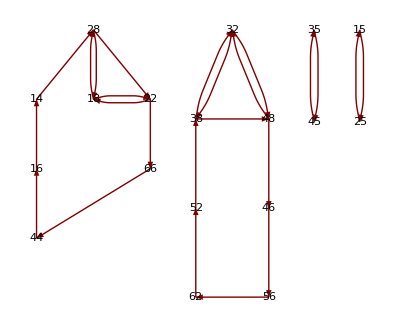

```mathematica
TreePlot[S71262252∪S35,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]
```

```mathematica
PermulateMultiply[StartSet,{5,5,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,6,6,11,6,6,2,2,2,6,6,11,6,6,2,2,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,2,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,1,7,10,7,10,7,1,1,5,5,3,3,14,3,3,5}]
```

{14→22,16→14,22→66,44→16,46→56,48→46,52→48,56→62,62→52,66→44}